## Algebraic Computation for Early Warnings Package

## Hopf initialisation parameters

```mathematica
Clear[smax,stot]
```

```mathematica
eqn1=smax == (σ^2/4Pi μ^2)*(1+μ^2/(μ^2+4 ω^2));
```

```mathematica
eqn2=stot==-σ^2/(2μ);
```

```mathematica
{eqn1,eqn2}
```

{smax==1/4 π μ^2 σ^2 (1+μ^2/(μ^2+4 ω^2)),stot==-σ^2/(2 μ)}

```mathematica
Clear[μ,ω,stot,smax]
eqn=4Pi smax μ^3 + 4 stot μ^2 + 16Pi smax ω^2 μ + 8stot ω^2 == 0
```

4 stot μ^2+4 π smax μ^3+8 stot ω^2+16 π smax μ ω^2==0

```mathematica
sol=Solve[eqn,μ][[1]]
```

{μ→-stot/(3 π smax)-(-16 stot^2+192 π^2 smax^2 ω^2)/(48 π smax (-stot^3-9 π^2 smax^2 stot ω^2+3 √3 π √(2 smax^2 stot^4 ω^2-13 π^2 smax^4 stot^2 ω^4+64 π^4 smax^6 ω^6))^(1/3))+1/(3 π smax)(-stot^3-9 π^2 smax^2 stot ω^2+3 √3 π √(2 smax^2 stot^4 ω^2-13 π^2 smax^4 stot^2 ω^4+64 π^4 smax^6 ω^6))^(1/3)}

```mathematica
μsol=μ/.sol
```

-stot/(3 π smax)-(-16 stot^2+192 π^2 smax^2 ω^2)/(48 π smax (-stot^3-9 π^2 smax^2 stot ω^2+3 √3 π √(2 smax^2 stot^4 ω^2-13 π^2 smax^4 stot^2 ω^4+64 π^4 smax^6 ω^6))^(1/3))+((-stot^3-9 π^2 smax^2 stot ω^2+3 √3 π √(2 smax^2 stot^4 ω^2-13 π^2 smax^4 stot^2 ω^4+64 π^4 smax^6 ω^6))^(1/3))/(3 π smax)

```mathematica
μsol//FullSimplify//TraditionalForm
```

1/(48 π smax)(16 (-9 π^2 smax^2 stot ω^2+3 π √(192 π^4 smax^6 ω^6-39 π^2 smax^4 stot^2 ω^4+6 smax^2 stot^4 ω^2)-stot^3)^(1/3)+(16 (stot^2-12 π^2 smax^2 ω^2))/((-9 π^2 smax^2 stot ω^2+3 π √(192 π^4 smax^6 ω^6-39 π^2 smax^4 stot^2 ω^4+6 smax^2 stot^4 ω^2)-stot^3)^(1/3))-16 stot)

```mathematica
Simplify
```

Simplify

```mathematica
μsol//Simplify
```

1/(48 π smax)(-16 stot+(16 (stot^2-12 π^2 smax^2 ω^2))/((-stot^3-9 π^2 smax^2 stot ω^2+3 π √(6 smax^2 stot^4 ω^2-39 π^2 smax^4 stot^2 ω^4+192 π^4 smax^6 ω^6))^(1/3))+16 (-stot^3-9 π^2 smax^2 stot ω^2+3 π √(6 smax^2 stot^4 ω^2-39 π^2 smax^4 stot^2 ω^4+192 π^4 smax^6 ω^6))^(1/3))

```mathematica
Root
```

Root

```mathematica
μ=μ/.sol[[1]]
```

-stot/(3 π smax)-(-16 stot^2+192 π^2 smax^2 ω^2)/(48 π smax (-stot^3-9 π^2 smax^2 stot ω^2+3 √3 π √(2 smax^2 stot^4 ω^2-13 π^2 smax^4 stot^2 ω^4+64 π^4 smax^6 ω^6))^(1/3))+((-stot^3-9 π^2 smax^2 stot ω^2+3 √3 π √(2 smax^2 stot^4 ω^2-13 π^2 smax^4 stot^2 ω^4+64 π^4 smax^6 ω^6))^(1/3))/(3 π smax)

### Investigate the arising cubic in μ

```mathematica
smax=1;
stot=3;
w0=1;
```

```mathematica
cubic[μ_,smax_,stot_,w0_]:=(-2*Pi*smax/stot)*μ^3 -2*μ^2 + (-8*Pi*smax*w0^2/stot)*μ-4*w0^2
```

```mathematica
Manipulate[Plot[cubic[μ,smax,stot,w0],{μ,-3,3},PlotRange->{-100,100}],
{smax,1,5},{stot,3,10},{w0,1,3}]
```

```mathematica
Clear[μ]
smax=1;
stot=4;
w0=3;
NSolve[cubic[μ,smax,stot,w0]==0,μ]
```

{{μ→-0.643867},{μ→-0.314686-5.95783 ⅈ},{μ→-0.314686+5.95783 ⅈ}}

```mathematica
Solve[cubic[μ,a,b,w]==0,μ,Reals]
```

{{μ→Root[2 b w^2+4 a π w^2 #1+b #1^2+a π #1^3&,1]}}

```mathematica
root = Solve[cubic[μ,a,b,w]==0,μ][[1]]
```

{μ→-b/(3 a π)+(-4 b^2+48 a^2 π^2 w^2)/(12 a π (b^3+9 a^2 b π^2 w^2+3 √3 π √(2 a^2 b^4 w^2-13 a^4 b^2 π^2 w^4+64 a^6 π^4 w^6))^(1/3))-((b^3+9 a^2 b π^2 w^2+3 √3 π √(2 a^2 b^4 w^2-13 a^4 b^2 π^2 w^4+64 a^6 π^4 w^6))^(1/3))/(3 a π)}

```mathematica
Clear[rootfun]
rootfun[a_,b_,w_]=μ/.root
```

-b/(3 a π)+(-4 b^2+48 a^2 π^2 w^2)/(12 a π (b^3+9 a^2 b π^2 w^2+3 √3 π √(2 a^2 b^4 w^2-13 a^4 b^2 π^2 w^4+64 a^6 π^4 w^6))^(1/3))-((b^3+9 a^2 b π^2 w^2+3 √3 π √(2 a^2 b^4 w^2-13 a^4 b^2 π^2 w^4+64 a^6 π^4 w^6))^(1/3))/(3 a π)

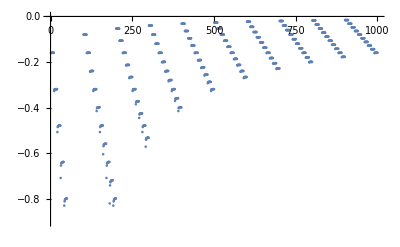

```mathematica
ListPlot[Table[rootfun[smax,stot,w0]//N,{smax,1,10},{stot,1,10},{w0,1,10}]//Flatten]
```

It looks like all the roots are behaving.

```mathematica
Root[cubic[#,1,3,1]&,1]
```

Root[6+4 π #1+3 #1^2+π #1^3&,1]